## Load packages and global definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../../Mathematica_packages/QMB.wl"]
Get["../../Mathematica_packages/Chaometer.wl"]
```

### Ticks

```mathematica
myTicksXBelow=Join[Table[{10.^i,Superscript[10,i],{0.015,0}},{i,-2,2}](*major ticks*),Flatten[Table[{10^i+j*10.^(i),"",{.005,0}},{i,-2,1},{j,1,8}],1](*minor ticks*)]
```

{{0.01,10^-2,{0.015,0}},{0.1,10^-1,{0.015,0}},{1.,10^0,{0.015,0}},{10.,10^1,{0.015,0}},{100.,10^2,{0.015,0}},{0.02,,{0.005,0}},{0.03,,{0.005,0}},{0.04,,{0.005,0}},{0.05,,{0.005,0}},{0.06,,{0.005,0}},{0.07,,{0.005,0}},{0.08,,{0.005,0}},{0.09,,{0.005,0}},{0.2,,{0.005,0}},{0.3,,{0.005,0}},{0.4,,{0.005,0}},{0.5,,{0.005,0}},{0.6,,{0.005,0}},{0.7,,{0.005,0}},{0.8,,{0.005,0}},{0.9,,{0.005,0}},{2.,,{0.005,0}},{3.,,{0.005,0}},{4.,,{0.005,0}},{5.,,{0.005,0}},{6.,,{0.005,0}},{7.,,{0.005,0}},{8.,,{0.005,0}},{9.,,{0.005,0}},{20.,,{0.005,0}},{30.,,{0.005,0}},{40.,,{0.005,0}},{50.,,{0.005,0}},{60.,,{0.005,0}},{70.,,{0.005,0}},{80.,,{0.005,0}},{90.,,{0.005,0}}}

```mathematica
myTicksXAbove=Join[Table[{10.^i,"",{0.015,0}},{i,-2,2}](*major ticks*),Flatten[Table[{10^i+j*10.^(i),"",{.005,0}},{i,-2,1},{j,1,8}],1](*minor ticks*)]
```

{{0.01,,{0.015,0}},{0.1,,{0.015,0}},{1.,,{0.015,0}},{10.,,{0.015,0}},{100.,,{0.015,0}},{0.02,,{0.005,0}},{0.03,,{0.005,0}},{0.04,,{0.005,0}},{0.05,,{0.005,0}},{0.06,,{0.005,0}},{0.07,,{0.005,0}},{0.08,,{0.005,0}},{0.09,,{0.005,0}},{0.2,,{0.005,0}},{0.3,,{0.005,0}},{0.4,,{0.005,0}},{0.5,,{0.005,0}},{0.6,,{0.005,0}},{0.7,,{0.005,0}},{0.8,,{0.005,0}},{0.9,,{0.005,0}},{2.,,{0.005,0}},{3.,,{0.005,0}},{4.,,{0.005,0}},{5.,,{0.005,0}},{6.,,{0.005,0}},{7.,,{0.005,0}},{8.,,{0.005,0}},{9.,,{0.005,0}},{20.,,{0.005,0}},{30.,,{0.005,0}},{40.,,{0.005,0}},{50.,,{0.005,0}},{60.,,{0.005,0}},{70.,,{0.005,0}},{80.,,{0.005,0}},{90.,,{0.005,0}}}

```mathematica
myTicksYLeft=Join[Table[{i,NumberForm[i,{3,2}],{.015,0}},{i,0.25,1,0.15}],Table[{i,"",{0.005,0}},{i,0.25,1,0.05}]]
```

{{0.25,0.25,{0.015,0}},{0.4,0.40,{0.015,0}},{0.55,0.55,{0.015,0}},{0.7,0.70,{0.015,0}},{0.85,0.85,{0.015,0}},{1.,1.00,{0.015,0}},{0.25,,{0.005,0}},{0.3,,{0.005,0}},{0.35,,{0.005,0}},{0.4,,{0.005,0}},{0.45,,{0.005,0}},{0.5,,{0.005,0}},{0.55,,{0.005,0}},{0.6,,{0.005,0}},{0.65,,{0.005,0}},{0.7,,{0.005,0}},{0.75,,{0.005,0}},{0.8,,{0.005,0}},{0.85,,{0.005,0}},{0.9,,{0.005,0}},{0.95,,{0.005,0}},{1.,,{0.005,0}}}

```mathematica
myTicksYRight=Join[Table[{i,"",{.015,0}},{i,0.25,1,0.15}],Table[{i,"",{0.005,0}},{i,0.25,1,0.05}]]
```

{{0.25,,{0.015,0}},{0.4,,{0.015,0}},{0.55,,{0.015,0}},{0.7,,{0.015,0}},{0.85,,{0.015,0}},{1.,,{0.015,0}},{0.25,,{0.005,0}},{0.3,,{0.005,0}},{0.35,,{0.005,0}},{0.4,,{0.005,0}},{0.45,,{0.005,0}},{0.5,,{0.005,0}},{0.55,,{0.005,0}},{0.6,,{0.005,0}},{0.65,,{0.005,0}},{0.7,,{0.005,0}},{0.75,,{0.005,0}},{0.8,,{0.005,0}},{0.85,,{0.005,0}},{0.9,,{0.005,0}},{0.95,,{0.005,0}},{1.,,{0.005,0}}}

## Calculos

```mathematica
L=9;(* number of spins *)
{J,hx,hz}={1,1,0.5};
```

Compute eigenvalues and eigenvectors of Hamiltonian:

```mathematica
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Chop[Eigensystem[IsingNNOpenHamiltonian[hx,hz,J,L]]]]]];
```

```mathematica
SeedRandom[20349];
ψE=RandomChainProductState[L-1];
```

```mathematica
t=Power[10,Range[-2,2,0.05]];
```

```mathematica
AbsoluteTiming[superoperators=Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L]]&/@t;]
```

{44.9982,Null}

```mathematica
chois=1/2*Reshuffle/@superoperators;
```

```mathematica
choiPurities=Chop[Purity/@chois];
```

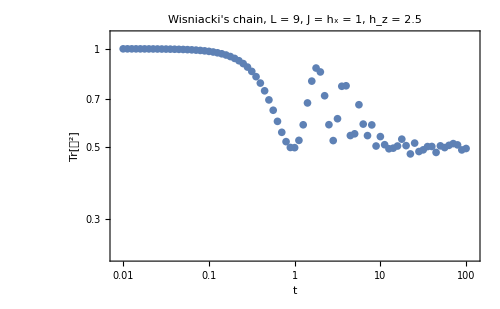

```mathematica
ListLogLogPlot[Transpose[{t,choiPurities}],
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->21],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,19],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Wisniacki's chain, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", J = h_x = 1, h_z = 2.5",
LabelStyle->Directive[Black,FontSize->17]
]
```

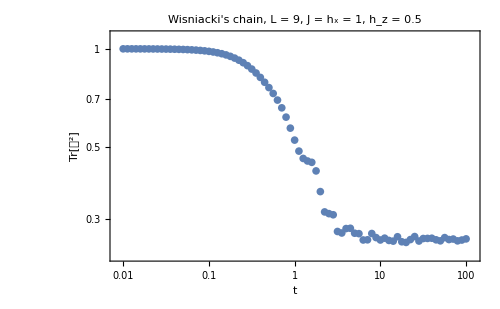

```mathematica
ListLogLogPlot[Transpose[{t,choiPurities}],
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->21],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,19],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Wisniacki's chain, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", J = h_x = 1, h_z = 0.5",
LabelStyle->Directive[Black,FontSize->17]
]
```

## Replacing the chaometer by another spin different than the left-most

```mathematica
L=9;(* number of spins *)
{J,hx,hz}={1,1,0.5};

superoperators={};

(* For the chaometer being each site of the chain, compute the superoperators of the channel *)
Do[
(* Compute eigenvalues and eigenvectors of spin chain's Hamiltonian *)
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Chop[Eigensystem[IsingNNOpenHamiltonian[hx,hz,J,L]]]]]];

(* Set the environent's initial state as a product random state *)
SeedRandom[20349];(*set a seed to always get the same random state ψE *)
ψE={RandomChainProductState[chaometer-1],RandomChainProductState[L-chaometer]};

AppendTo[superoperators,Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L,chaometer]]&/@t];
,{chaometer,9}]
```

Show the nine data points in the same plot:

```mathematica
chois=1/2Map[Reshuffle,superoperators,{2}];
```

```mathematica
choiPurities=Chop[Map[Purity,chois,{2}]];
```

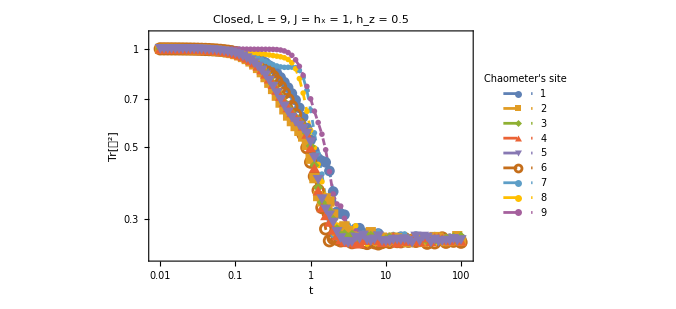

```mathematica
fig=ListLogLogPlot[Transpose[{t,#}]&/@choiPurities,
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Joined->True,PlotStyle->Directive[Dashed],PlotMarkers->Automatic,
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,20],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Closed, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", J = h_x = "<>ToString[J]<>", h_z = "<>ToString[hz],
LabelStyle->Directive[Black,FontSize->19],
ImagePadding->{{Automatic,Automatic},{Automatic,5}},
PlotLegends->LineLegend[ToString[#]&/@Range[9],LegendLabel->Placed["Chaometer's site",Above]]
]
```

```mathematica
Export["../figs_ja/wisniacki/varying_chaometers_site/L_9_J_hx_1_hz_0.5.pdf",fig]
```

../figs_ja/wisniacki/varying_chaometers_site/L_9_J_hx_1_hz_0.5.pdf

## Closed chain

```mathematica
?IsingNNClosedHamiltonian
```

```mathematica
L=9;(* number of spins *)
{J,hx,hz}={1,1,0.5};

superoperators={};

(* For the chaometer being each site of the chain, compute the superoperators of the channel *)
Do[
(* Compute eigenvalues and eigenvectors of spin chain's Hamiltonian *)
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Chop[Eigensystem[IsingNNClosedHamiltonian[hx,hz,J,L]]]]]];

(* Set the environent's initial state as a product random state *)
SeedRandom[20349];(*set a seed to always get the same random state ψE *)
ψE={RandomChainProductState[chaometer-1],RandomChainProductState[L-chaometer]};

AppendTo[superoperators,Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L,chaometer]]&/@t];
,{chaometer,9}]
```

```mathematica
chois=1/2Map[Reshuffle,superoperators,{2}];
```

```mathematica
choiPurities=Chop[Map[Purity,chois,{2}]];
```

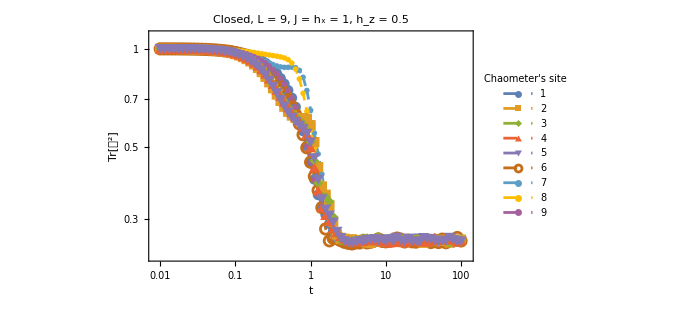

```mathematica
fig=ListLogLogPlot[Transpose[{t,#}]&/@choiPurities,
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Joined->True,PlotStyle->Directive[Dashed],PlotMarkers->Automatic,
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,20],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Closed, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>", J = h_x = "<>ToString[J]<>", h_z = "<>ToString[hz],
LabelStyle->Directive[Black,FontSize->19],
ImagePadding->{{Automatic,Automatic},{Automatic,5}},
PlotLegends->LineLegend[ToString[#]&/@Range[9],LegendLabel->Placed["Chaometer's site",Above]]
]
```

```mathematica
Export["../figs_ja/wisniacki/varying_chaometers_site/closed_L_9_J_hx_1_hz_0.5.pdf",fig]
```

../figs_ja/wisniacki/varying_chaometers_site/closed_L_9_J_hx_1_hz_0.5.pdf